# Little Tests

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{NotebookDirectory[],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedSteps","ConstrainedInitialSignLeft","ConstrainedInitialSignStepsLeft","ConstrainedInitialSignStepsRight"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"bamboo_1","0001",r,"clean"];

(* {1,44},{1,102} arbitrary size to make the method faster *)
nx=150/r;
ny=300/r;
{ia,ib,id,io}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id,io}
ImageDimensions[#]&/@{ia,ib,id,io}

max=MinMax[Flatten[ImageData[id]]][[2]];
Print["max dv=", max]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45},{103,45}}

max dv=12.5952

## Little Tests

#### Little Functions

```mathematica
pyrfi[ia_,ib_,row_,lvlmax_]:=Block[{pyrfia,pyrfib},
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvlmax];
pyrfib=pyrFuncGen[ImageData[ib][[row]],lvlmax];

Flatten[{pyrfia,pyrfib},{{2},{1},{3}}]
]
```

```mathematica
row=20;
lvlmin=1;
lvlmax=4;

pyrfiab=pyrfi[ia,ib,row,lvlmax];
```

#### Little Test: Friction

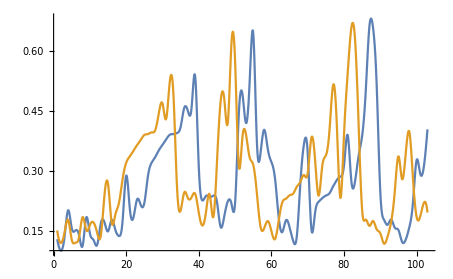

```mathematica
Plot[{pyrfiab[[1,1,1]][x],pyrfiab[[1,2,1]][x]},{x,1,103}]
```

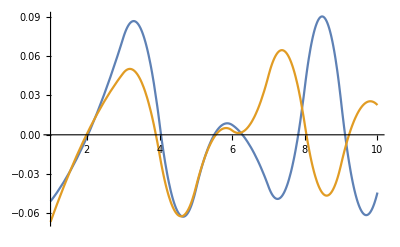

```mathematica
Plot[{pyrfiab[[1,1,2]][x],pyrfiab[[1,2,2]][x]},{x,1,10}]
```

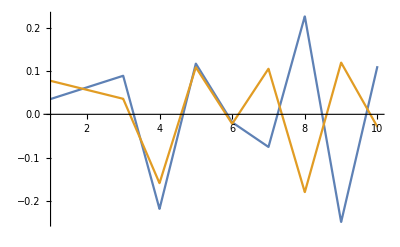

```mathematica
Plot[{pyrfiab[[1,1,2]]'[x],pyrfiab[[1,2,2]]'[x]},{x,1,10}]
```

#### Little Test: All packages

```mathematica
row=20;
lvlmin=3;
lvlmax=4;

pyrfiab=pyrfi[ia,ib,row,lvlmax-1];
```

```mathematica
e=0.01;
```

```mathematica
(* Check solution *)
ic=(*move[ia,-dv]*)ib;
```

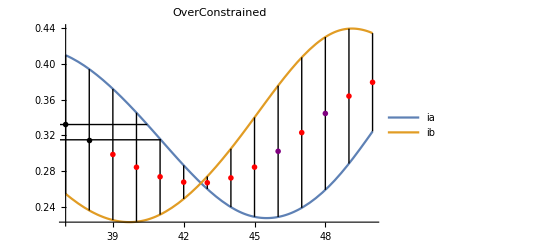

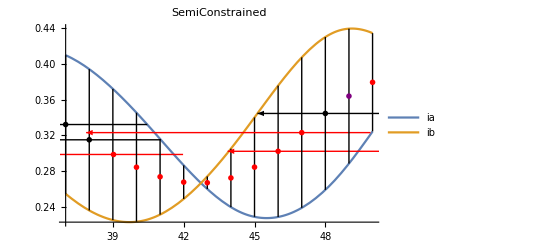

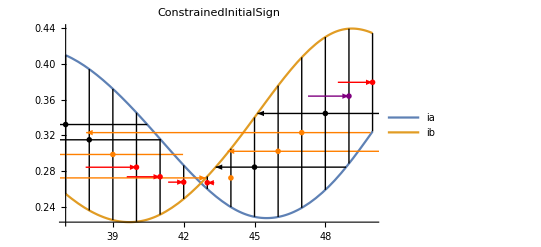

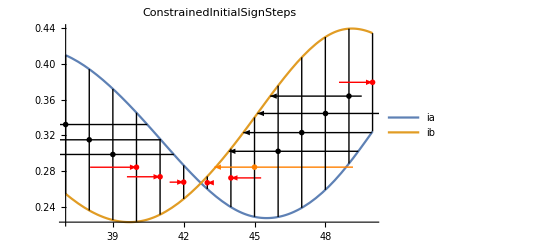

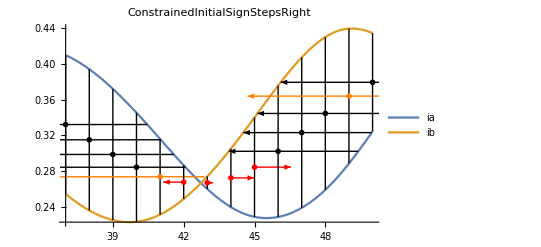

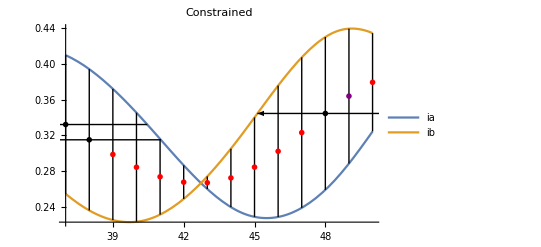

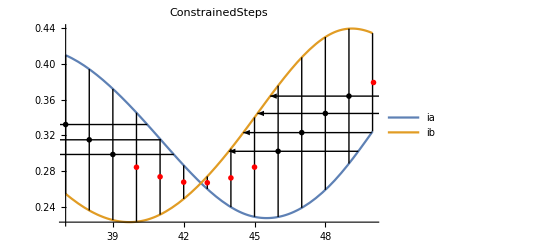

```mathematica
rangex=Range[37,50];

mode="OverConstrained";
seeAllLine[rangex,pyrfiab[[lvlmin;;lvlmax]],0.01*2^(-lvlmin+1),mode]
mode="SemiConstrained";
seeAllLine[rangex,pyrfiab[[lvlmin;;lvlmax]],0.01*2^(-lvlmin+1),mode]
mode="ConstrainedInitialSign";
seeAllLine[rangex,pyrfiab[[lvlmin;;lvlmax]],0.01*2^(-lvlmin+1),mode]
mode="ConstrainedInitialSignSteps";
seeAllLine[rangex,pyrfiab[[lvlmin;;lvlmax]],(0.01/3)*2^(-lvlmin+1),mode]
mode="ConstrainedInitialSignStepsRight";
seeAllLine[rangex,pyrfiab[[lvlmin;;lvlmax]],(0.01/3)*2^(-lvlmin+1),mode]
mode="Constrained";
seeAllLine[rangex,pyrfiab[[lvlmin;;lvlmax]],0.01*2^(-lvlmin+1),mode]
mode="ConstrainedSteps";
seeAllLine[rangex,pyrfiab[[lvlmin;;lvlmax]],(0.01/3)*2^(-lvlmin+1),mode]
```

#### Little Test: ConstrainedInitialSign Animation

```mathematica
p=40;
```

```mathematica
mode="ConstrainedInitialSign";
ListAnimate[pixelIterGraphics[10,p,{0,0},30, lvlmax,pyrfiab[[lvlmin;;lvlmax]],0.01*2^(-lvlmin+1),mode]]
```

```mathematica
mode="ConstrainedInitialSignSteps";
ListAnimate[pixelIterGraphics[10,p,{0,0},30, lvlmax,pyrfiab[[lvlmin;;lvlmax]],(0.01)*2^(-lvlmin+1),mode]]
```

$Aborted

```mathematica
mode="ConstrainedSteps";
ListAnimate[pixelIterGraphics[10,p,{0,0},30, lvlmax,pyrfiab[[lvlmin;;lvlmax]],(0.01)*2^(-lvlmin+1),mode]]
```